## Input Data

```mathematica
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
Off[SixJSymbol::tri];
Off[SixJSymbol::phy];
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[SixJSymbol::tri]];
ParallelEvaluate[Off[Infinity::indet]];
ParallelEvaluate[Off[ClebschGordan::phy]];
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[NIntegrate::eincr]];
ParallelEvaluate[Off[NIntegrate::slwcon]];
ParallelEvaluate[Off[General::munfl ]];
SetDirectory[StringJoin[NotebookDirectory[]]]
```

/Users/zhan/bsmllh/nb/theDD

```mathematica
m={4.,1.,1.};
fileName="li/li0";
importedData=Import[FileNameJoin[{NotebookDirectory[], StringJoin[fileName,".wf"]}], "Table"];
γ={};
dataList={};
tempList={};
AppendTo[γ,importedData⟦1⟧];
Do[
If[IntegerQ@importedData⟦i,1⟧,
AppendTo[γ,importedData⟦i⟧];
AppendTo[dataList,tempList];
tempList={};
,
AppendTo[tempList,importedData⟦i⟧];
];
,{i,2,Length@importedData}];
AppendTo[dataList,tempList];
Clear[tempList];
```

```mathematica
Cij={};
αij={};
βij={};
Do[
tempCij={};
tempαij={};
tempβij={};
Do[
If[i==j,AppendTo[tempCij,dataList⟦k,i,3⟧dataList⟦k,j,3⟧]
,AppendTo[tempCij,2dataList⟦k,i,3⟧dataList⟦k,j,3⟧]];
AppendTo[tempαij,2(dataList⟦k,i,1⟧+dataList⟦k,j,1⟧)];
AppendTo[tempβij,2(dataList⟦k,i,2⟧+dataList⟦k,j,2⟧)];
,{i,1,Length@dataList⟦k,All,3⟧},{j,1,i}];
AppendTo[Cij,tempCij];
AppendTo[αij,tempαij];
AppendTo[βij,tempβij];
,{k,1,Length@γ}];
```

```mathematica
(*T=Module[{c,s},
c=-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)));
s=(-1)^(2-1)Sign[1-2] √(1-c^2);
{{c,s},{-s,c}}];*)
(*T={{-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))},{√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))}};*)
(*T={{-m⟦2⟧/(m⟦2⟧+m⟦3⟧),1},{-(m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦2⟧+m⟦3⟧)(m⟦1⟧+m⟦3⟧)),-m⟦1⟧/(m⟦1⟧+m⟦3⟧)}};*)
T={{-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))},{√((m⟦3⟧(m⟦1⟧+m⟦2⟧+m⟦3⟧))/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧))),-√((m⟦1⟧m⟦2⟧)/((m⟦1⟧+m⟦3⟧)(m⟦2⟧+m⟦3⟧)))}};
Q=T.{{1,p},{0,1}};
Protect[p];
Det[T]
μij=T⟦1,1⟧^2 αij+T⟦2,1⟧^2 βij;
νij=T⟦1,2⟧^2 αij+T⟦2,2⟧^2 βij;
ρij=(T⟦1,1⟧T⟦1,2⟧αij+T⟦2,1⟧T⟦2,2⟧βij);
ωij=νij-ρij^2/μij;
```

1.

## Independence of the y angular variables in Exp

```mathematica
𝒾[l_,x_]:=√(Pi/(2 x))BesselI[l+1/2,x];
With[{x={0.91,xTh,xPh},y={0.5,0.5,0.516}},
{4Pi 𝒾[0,x⟦1⟧ y⟦1⟧],
NIntegrate[Sin[xTh]Exp[FromSphericalCoordinates[x].FromSphericalCoordinates[y]],{xTh,0,Pi},{xPh,0,2Pi}]}]
```

{13.0045,13.0045}

## an Eq. from the Varga Suzuki book

```mathematica
ℐ[n_,l_,ν_,ω_]:=√(Pi/2)((2n)!!ω^l)/ν^(n+l+3/2)Exp[ω^2/(2ν)]LaguerreL[n,l+1/2,-ω^2/(2ν)];
ℐ[n_,a_]:=Gamma[1/2+n/2]/(2 a^(1/2+n/2));(*Integrate[x^n Exp[-a x^2],{x,0,Infinity}]*)
With[{n=1,l=0,ν=1.2,ω=0.654, y0=1.2^-1},
Print[ℐ[n,l,y0^2 ν,y0 ω]];
Print[NIntegrate[y^(2n+l+2)Exp[-1/2 ν (y0 y)^2]𝒾[l,ω y0 y],{y,0,Infinity}]];
]
```

7.93028

7.93028

## Normalization of each partial wave and the total wave function

```mathematica
Total[Cij⟦#⟧ℐ[2+2γ⟦#,1⟧,1/2 αij⟦#⟧]ℐ[2+2γ⟦#,2⟧,1/2 βij⟦#⟧]]&/@Range[1,Length@Cij];
𝒩=%
Total@%
```

{0.898178135446813,0.07325780768793994,0.021071679803573858,0.00479067147184594605,0.00161404128936349683,0.0004864006123102972983,0.000601263687847505337}

0.999999999999694

```mathematica
γForCalc=Flatten[Position[𝒩,_?(#>0.1&)]]
```

{1}

## Some needed formulas

```mathematica
𝒴[j1_,j2_,j_,x_,y_]:=Sum[ClebschGordan[{j1,jm1},{j2,jm2},{j,j}]
SphericalHarmonicY[j1,jm1,x⟦2⟧,x⟦3⟧]SphericalHarmonicY[j2,jm2,y⟦2⟧,y⟦3⟧],{jm1,-j1,j1},{jm2,-j2,j2}];
uNineJ[{{a_, b_, c_}, {d_, e_, f_}, {g_, h_, j_}}]:=Total[√((2c+1)(2f+1)(2g+1)(2h+1))(-1)^(2#)(2#+1)SixJSymbol[{a,b,c},{f,j,#}]SixJSymbol[{d,e,f},{b,#,h}]SixJSymbol[{g,h,j},{#,a,d}]&/@Range[0,4]];
ℭ[l1_,l2_,L_]:=√(((2l1+1)(2l2+1))/(4Pi (2L+1)))ClebschGordan[{l1,0},{l2,0},{L,0}];
𝔇[l1_,l2_,L_]:=√((4Pi (2L+1)!)/((2l1+1)!(2l2+1)!));
𝔈[{{a_, b_, c_}, {d_, e_, f_}, {g_, h_, j_}}]:=uNineJ[{{a, b, c}, {d, e, f}, {g, h, j}}]ℭ[a,d,g]ℭ[b,e,h];
triQ[a_,b_,c_]:=If[Abs[a-b]≤c≤a+b&&Abs[a-c]≤b≤a+c&&Abs[b-c]≤a≤b+c,True,False];
```

```mathematica
𝒴2ij[k_,x_,y_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,j91,j92,dataList={},inc},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/μij⟦k⟧})
x⟦1⟧^(λ1i+l1i+λ1j+l1j)y⟦1⟧^(2λ+2l-λ1i-l1i-λ1j-l1j)Exp[-1/2(μij⟦k⟧)(x⟦1⟧)^2-1/2(ωij⟦k⟧)(y⟦1⟧)^2];
(*AppendTo[dataList,𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]];*)
(*Print[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}},"\t",{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}];*)
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
sum
];
```

```mathematica
W2[k_,x_,y_]:=Total[Cij⟦k⟧ x^2 y^2 𝒴2ij[k,{x,1,1},{y,1,1}]];
```

```mathematica
(*NIntegrate[W2[2,x,y],{x,0,Infinity},{y,0,Infinity}]*)
```

## checking the DD function

```mathematica
(*Block[{aij=0.6456,Cij=1.39 ,bij=0.9341,λ=2,l=1,
y={yr,yTh,yPh},R={3.45,rTh,rPh},ρ0=0.4229 ,γ0=0.7024,ρα,ϕ,y0=1.2^-1,
E1,E2,E3},
ρα[r_]:=ρ0 Exp[- γ0 r.r];
ϕ[r_]:=Cij r⟦1⟧^(2l)Exp[-1/2bij r.r];
E1=ℐ[2+2λ,aij]NIntegrate[
(yr)^2 Sin[yTh]Sin[rTh]
ρα[FromSphericalCoordinates[R]-y0 FromSphericalCoordinates[y]]
ϕ[{ y⟦1⟧,0,0}]
,{yr,0,Infinity},{yTh,0,Pi},{yPh,0,2Pi},{rTh,0,Pi},{rPh,0,2Pi}];
E2=(4Pi)^2 Cij ρ0 Exp[-γ0  R⟦1⟧^2] ℐ[2+2λ,aij]ℐ[l,0,(bij +2 y0^2 γ0),2γ0  y0 R⟦1⟧];
{E1,E2}
]*)
```

## the DDNM of the first cluster

```mathematica
rMax=10.5;
hInt=0.3;
```

```mathematica
ρ1α[k_,R_]:=With[{ρ0=0.4229 ,γ0=0.641(*0.7024*),λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))},
(4Pi)^2 Total[Cij⟦k⟧ ρ0 Exp[-γ0 R^2] ℐ[2+2λ,1/2 αij⟦k⟧]ℐ[l,0,(βij⟦k⟧+2 y0^2 γ0),2γ0 y0 R]]];
ρ1n[k_,R_]:=With[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,y0=((m⟦2⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-1},
Total[Cij⟦k⟧  R^(2+2l)ℐ[2+2λ,1/2 αij⟦k⟧]Exp[-1/2 βij⟦k⟧(y0 R)^2]]];


Block[{iFunction,data},
data=If[m⟦1⟧==1.,
Table[{R,Total[ρ1n[#,R]&/@γForCalc]},{R,10^-5,rMax,hInt}],
If[m⟦1⟧==4.,Table[{R,Total[ρ1α[#,R]&/@γForCalc]},{R,10^-5,rMax,hInt}]]
];
ρ1=Interpolation[data];
];
𝒩1=m⟦1⟧(4Pi NIntegrate[ρ1[r] r^2,{r,10^-5,rMax}])^-1;
```

## the DDNM for the second cluster

```mathematica
ρ2n[k_,y_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,j91,j92,dataList={},inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧))^-1},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/μij⟦k⟧})
y^(2λ+2l-λ1i-l1i-λ1j-l1j+2)Exp[-1/2(ωij⟦k⟧)(y0 y)^2]ℐ[λ1i+l1i+λ1j+l1j+2,1/2(μij⟦k⟧)];
(*y^(2λ+2l-λ1i-l1i-λ1j-l1j+2)Exp[-1/2(ωij⟦k⟧)(y0 y)^2]ℐ[λ1i+l1i+λ1j+l1j+2,1/2(μij⟦k⟧)];*)
(*AppendTo[dataList,𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]];*)
(*Print[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}},"\t",{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}];*)
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
Total[Cij⟦k⟧sum]
];

ρ2α[k_,R_]:=Block[{λ=γ⟦k,1⟧,l=γ⟦k,2⟧,L=γ⟦k,3⟧,sum=0.0,inc,y0=((m⟦1⟧+m⟦3⟧)/(m⟦1⟧+m⟦2⟧+m⟦3⟧)),ρ0=0.4229 ,γ0=0.641(*0.7024*)},
Do[
If[!triQ[λ1i,λ-λ1i,λ],Continue[]];
If[!triQ[l1i,l-l1i,l],Continue[]];
If[!triQ[λ-λ1i,l-l1i,ℓ2],Continue[]];
If[!triQ[λ1i,l1i,ℓ1],Continue[]];
If[!triQ[λ,l,L],Continue[]];
If[!triQ[ℓ1,ℓ2,L],Continue[]];
If[!triQ[λ1j,λ-λ1j,λ],Continue[]];
If[!triQ[l1j,l-l1j,l],Continue[]];
If[!triQ[λ-λ1j,l-l1j,ℓ2],Continue[]];
If[!triQ[λ1j,l1j,ℓ1],Continue[]];
inc=𝔈[{{λ1i, λ-λ1i, λ}, {l1i, l-l1i, l}, {ℓ1, ℓ2, L}}]𝔈[{{λ1j, λ-λ1j, λ}, {l1j, l-l1j, l}, {ℓ1, ℓ2, L}}] 
𝔇[λ1i,λ-λ1i,λ]𝔇[l1i,l-l1i,l]𝔇[λ1j,λ-λ1j,λ]𝔇[l1j,l-l1j,l] 
Q⟦1,1⟧^(λ1i+λ1j)Q⟦2,1⟧^(l1i+l1j)( Q⟦1,2⟧^(2λ-λ1i-λ1j)Q⟦2,2⟧^(2l-l1i-l1j) /.{p->-ρij⟦k⟧/μij⟦k⟧})
ℐ[(2λ+2l-λ1i-l1i-λ1j-l1j)/2,0,(ωij⟦k⟧+2γ0 y0^2),2γ0 y0  R]ℐ[λ1i+l1i+λ1j+l1j+2,1/2(μij⟦k⟧)];
sum+=inc;
,{λ1i,0,λ},{l1i,0,l},{λ1j,0,λ},{l1j,0,l},{ℓ1,0,l+λ},{ℓ2,0,l+λ-ℓ1}];
ρ0 Exp[-γ0 R^2]Total[Cij⟦k⟧sum]
];

Block[{iFunction,data},
data=If[m⟦2⟧==1.,
ParallelTable[{R,Total[ρ2n[#,R]&/@γForCalc]},{R,10^-5,rMax,hInt}],
If[m⟦2⟧==4.,ParallelTable[{R,Total[ρ2α[#,R]&/@γForCalc]},{R,10^-5,rMax,hInt}]]
];
ρ2=Interpolation[data];
];
𝒩2=2m⟦2⟧(4Pi NIntegrate[ρ2[r] r^2,{r,10^-5,rMax}])^-1;
```

```mathematica
colorFunction={ColorData[97,"ColorList"]⟦2⟧,ColorData[97,"ColorList"]⟦1⟧};
If[Characters[fileName]⟦1⟧=="b",
colorFunction={ColorData[97,"ColorList"]⟦1⟧,ColorData[97,"ColorList"]⟦2⟧};
];
```

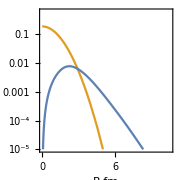

2.70

```mathematica
graph1=LogPlot[{𝒩1 ρ1[r],𝒩2 ρ2[r]},{r,10^-3,rMax},Frame->True,AspectRatio->1,PlotRange->{Automatic,{10^-5,0.6}},ImageSize->Small,FrameLabel->{"R,fm","ρ(R),fm^-3"},PlotStyle->colorFunction]
rms=NumberForm[(NIntegrate[( 𝒩1 ρ1[r]+𝒩2 ρ2[r])r^4,{r,10^-3,rMax}]/NIntegrate[(𝒩1 ρ1[r]+𝒩2 ρ2[r])r^2,{r,10^-3,rMax}])^(1/2),{3,2}]
```

```mathematica
Export[StringJoin[fileName,"_theDD",".pdf"],graph1,"pdf"];
```

```mathematica
StringRiffle[γ⟦#⟧]&/@Range[Length@γ];
Transpose[{%,NumberForm[#,{4,3}]&/@𝒩}] ;
StringJoin["<rms>^1/2_m = ",ToString[rms],"\n",StringRiffle[%]]
Export[StringJoin[fileName,".norm"],%,"Text"];
```

<rms>^1/2_m = 2.70
0 0 0 1 0.898
2 0 2 1 0.073
1 1 1 0 0.021
2 2 0 1 0.005
2 2 1 1 0.002
2 2 2 1 0.000
0 2 2 1 0.000

```mathematica
(*graph2=ContourPlot[Sum[x^(2+2γ⟦k,1⟧)y^(2+2γ⟦k,2⟧)Total[Cij⟦k⟧Exp[-1/2αij⟦k⟧x^2-1/2 βij⟦k⟧y^2]],{k,γForCalc}],{x,0.1,8},{y,0.1,8},PlotRange->Full,AspectRatio->1.,ImageSize->Small,FrameLabel->{"x","y"},PlotLabel->"x^2y^2|Ψ(x,y)|^2"]*)
```

```mathematica
(*Export[StringJoin[fileName,"_theCP",".jpg"],graph2,"jpg",ImageResolution->1000];*)
```

```mathematica
(*graph3=Plot3D[Sum[x^(2+2γ⟦k,1⟧)y^(2+2γ⟦k,2⟧)Total[Cij⟦k⟧Exp[-1/2αij⟦k⟧x^2-1/2 βij⟦k⟧y^2]],{k,γForCalc}],{x,0,8},{y,0,8},PlotRange->Full,AspectRatio->1.5,PerformanceGoal->"Quality",ImageSize->Small,AxesLabel->{"x, fm","y, fm"},PlotLabel->"x^2y^2|Ψ(x,y)|^2"]*)
```

```mathematica
(*Export[StringJoin[fileName,"_the3D",".jpg"],graph3,"jpg",ImageResolution->1000];*)
```

```mathematica
f77Eform[x_?NumericQ,fw_Integer,ndig_Integer]:=Module[{sig,s,p,ps},{s,p}=MantissaExponent[x];
{sig,ps}={ToString[Round[10^ndig Abs[s]]],ToString[Abs[p]]};
StringJoin@@Join[Table[" ",{fw-ndig-7}],If[x<0,"-"," "],{"0."},{sig},Table["0",{ndig-StringLength[sig]}],{"E"},If[p<0,{"-"},{"+"}],Table["0",{2-StringLength[ps]}],{ps}]];
```

```mathematica
(*Do[
Print["\\midrule"];
rowString=StringJoin["\\multicolumn{4}{c}{ $\\gamma \\equiv $  ", StringRiffle[γ⟦k⟧],"} \\\\"];
Print[rowString];
Print["\\midrule"];
Do[
Print[StringJoin[ToString[i],"  &  ", ToString[NumberForm[2.dataList⟦k,i,1⟧,{8,8}]],"  &  ", ToString[NumberForm[2.dataList⟦k,i,2⟧,{8,8}]], "  &  ",  ToString[f77Eform[dataList⟦k,i,3⟧,10,10]] ," \\\\"]];
,{i,1,Length@dataList⟦k,All,3⟧}];
,{k,1,Length@dataList⟦All,1,3⟧}];*)
```

## Export density functions

```mathematica
Block[{r,rMin=0.01,rMax=10.01,rH=10.0/200.,tot, k,p},
r=Table[NumberForm[r,{4,4}],{r,rMin,rMax,rH}];
Print[r];
tot=Transpose@{r,Table[f77Eform[𝒩1 ρ1[r]+𝒩2 ρ2[r],6,6],{r,rMin,rMax,rH}]};
k=Transpose@{r,Table[f77Eform[𝒩1 ρ1[r],6,6],{r,rMin,rMax,rH}]};
p=Transpose@{r,Table[f77Eform[𝒩2 ρ2[r],6,6],{r,rMin,rMax,rH}]};
Export[StringJoin[fileName,"_tot.ddt"],tot,"Table"];
Export[StringJoin[fileName,"_k.ddt"],k,"Table"];
Export[StringJoin[fileName,"_p.ddt"],p,"Table"];
{rMax, rMin,rH}
]
```

{0.0100,0.0600,0.1100,0.1600,0.2100,0.2600,0.3100,0.3600,0.4100,0.4600,0.5100,0.5600,0.6100,0.6600,0.7100,0.7600,0.8100,0.8600,0.9100,0.9600,1.0100,1.0600,1.1100,1.1600,1.2100,1.2600,1.3100,1.3600,1.4100,1.4600,1.5100,1.5600,1.6100,1.6600,1.7100,1.7600,1.8100,1.8600,1.9100,1.9600,2.0100,2.0600,2.1100,2.1600,2.2100,2.2600,2.3100,2.3600,2.4100,2.4600,2.5100,2.5600,2.6100,2.6600,2.7100,2.7600,2.8100,2.8600,2.9100,2.9600,3.0100,3.0600,3.1100,3.1600,3.2100,3.2600,3.3100,3.3600,3.4100,3.4600,3.5100,3.5600,3.6100,3.6600,3.7100,3.7600,3.8100,3.8600,3.9100,3.9600,4.0100,4.0600,4.1100,4.1600,4.2100,4.2600,4.3100,4.3600,4.4100,4.4600,4.5100,4.5600,4.6100,4.6600,4.7100,4.7600,4.8100,4.8600,4.9100,4.9600,5.0100,5.0600,5.1100,5.1600,5.2100,5.2600,5.3100,5.3600,5.4100,5.4600,5.5100,5.5600,5.6100,5.6600,5.7100,5.7600,5.8100,5.8600,5.9100,5.9600,6.0100,6.0600,6.1100,6.1600,6.2100,6.2600,6.3100,6.3600,6.4100,6.4600,6.5100,6.5600,6.6100,6.6600,6.7100,6.7600,6.8100,6.8600,6.9100,6.9600,7.0100,7.0600,7.1100,7.1600,7.2100,7.2600,7.3100,7.3600,7.4100,7.4600,7.5100,7.5600,7.6100,7.6600,7.7100,7.7600,7.8100,7.8600,7.9100,7.9600,8.0100,8.0600,8.1100,8.1600,8.2100,8.2600,8.3100,8.3600,8.4100,8.4600,8.5100,8.5600,8.6100,8.6600,8.7100,8.7600,8.8100,8.8600,8.9100,8.9600,9.0100,9.0600,9.1100,9.1600,9.2100,9.2600,9.3100,9.3600,9.4100,9.4600,9.5100,9.5600,9.6100,9.6600,9.7100,9.7600,9.8100,9.8600,9.9100,9.9600,10.0100}

{10.01,0.01,0.05}